```mathematica
vr[r_,θ_]:=  R[r] Cos[θ];
uθ[r_,θ_]:= Θ[r] Sin[θ];
uz[r_,θ_]:=0.0;
pL[r_,θ_]:=μ P[r] Cos[θ];
```

Boundary condition are all identically satisfied if the part of conditions is independent of θ:

```mathematica
R[b] = U; Θ[b] = -U;
```

The part of the boundary conditions independent of y are then satisfied if:

```mathematica
R[a]=0;aΘ'[a] = Θ[a] + R[a];
```

Solutions are:

```mathematica
R[r_] := (2 Log[r/a] (a^4+b^4)-b^2(r^2-a^4/r^2))/(2Log[b/a](a^4+b^4)-(b^4-a^4))U;
Θ[r_]:=- (2 Log[r/a] (a^4+b^4)+2(a^4+b^4)-b^2(3 r^2+a^4/r^2))/(2 Log[b/a](a^4+b^4)-(b^4-a^4))U;
P[r_]:= -4(2 r b^2 +(a^4+b^4)/r)/(2 Log[b/a](a^4+b^4)-(b^4-a^4))U;
```

Likewise a z-dependent portion to the solution of the form:

```mathematica
vr[z_,r_]:= Cos[(n π z)/h] Rn[r];
uθ[z_,r_]:= 0;
uz[z_,r_]:=Sin[n π z/h]Zn[r];
pl[z_,r_]:= Subscript[μ, E] Cos[(n π z)/h]Pn[r];
```

```mathematica
Pn[rn_]:=(2 n π)/h(A BesselK[0,rn] + B BesselI[0,rn]);
Rn[rn_]:= A rn BesselK[0,rn] + B rn BesselI[0,rn]+𝒞 BesselK[1,rn] + 𝒟 BesselI[1,rn];
Zn[rn_]:= A *(rn BesselK[1,rn]-2 BesselK[0,rn])-B*(rn BesselI[1,rn]+2 BesselI[0,rn])+𝒞 BesselK[0,rn]-𝒟*BesselI[0,rn];
```

Simple special case where the weld pool is so large that S/L boundary can be considered arbitrarily far away:

```mathematica
A=(-w0 γ h^2)/(π^2 a^2 μ)* 1/(n^2 BesselK[1,n π a/h]);
𝒞=(w0 γ h)/(π a μ)*BesselK[0,n π a/h]/(n(BesselK[1,n π a/h])^2);
B=0; 𝒟=0;
```

```mathematica
w0=1; γ=0.1; a=1; h=10; b=10;μ=0.2; n=2;
```

```mathematica
A
```

-20.9477

```mathematica
𝒟
```

0

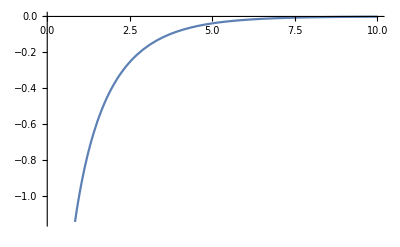

```mathematica
Plot[Pn[n π r/h],{r,0.1,10}]
```

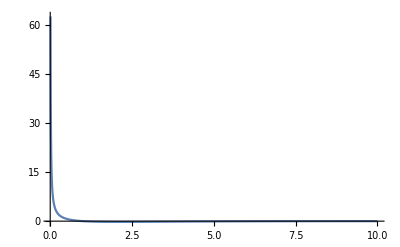

```mathematica
Plot[Rn[n π r/h],{r,0.01,10},PlotRange->All]
```

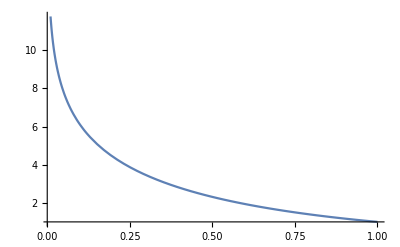

```mathematica
Plot[Zn[n π r/h],{r,0.01,1},PlotRange->All]
```

The final solutions are given as combinations of the results:

```mathematica
ur[r0_,z_,θ_]:=Module[{rn = n π r0/h, an= n π a/h, zn=n π z/h, Up = τ h/(U π μ),a=a/h,b=b/h,r=r0/h},
(*Print[∑_(i=1)^100 ((rn BesselK[0,rn])/(an BesselK[1,an])-(BesselK[0,an] BesselK[1,rn])/BesselK[1,an]^2) Cos[zn]/i];*)
(2 Log[r/a](a^4+b^4)-b^2(r^2-a^4/r^2))/(2 Log[b/a](a^4+b^4)-(b^4-a^4))Cos[θ]-
Up ∑_(i=1)^10 ((rn BesselK[0,rn])/(an BesselK[1,an])-(BesselK[0,an] BesselK[1,rn])/BesselK[1,an]^2) Cos[zn]/i];
uθ[r0_,θ_]:=Module[{a=a/h,b=b/h,r=r0/h},- (2(Log[r/a]+1)(a^4+b^4)-b^2(3 r^2+a^4/r^2))/(2 Log[b/a](a^4+b^4)-(b^4-a^4))Sin[θ]];
uz[r_,z_,θ_]:= Module[{rn=n π r/h, an = n π a/h, zn = n π z/h, Up=τ h/(U π μ),sumz=0}, sumz=∑_(i=1)^10 (rn/an BesselK[1,rn]/BesselK[1,an]-BesselK[0,rn]*((an*BesselK[0,an]+2 BesselK[1,an])/(an BesselK[1,an]^2)))Sin[zn]/i;
-Up sumz];
```

```mathematica
U=1;τ=.1;
```

```mathematica
uz[0.01,0.01,1.2]
```

0.432503

```mathematica
uθ[0.01,1.2]
```

27.7128

```mathematica
ur[coord1[[1]],coord1[[2]],coord1[[3]]]
```

4.78829×10^-19

0.601257

```mathematica
Convert[r_,θ_, z_,t_]:= {(ur[r,z,θ] Cos[θ]-uθ[r,θ] Sin[θ])t, (ur[r,z,θ] Sin[θ]+uθ[r,θ] Cos[θ])*t, uz[r,z,θ]*t};
```

```mathematica
Convert2d[r_,θ_, z_,t_]:={(ur[r,z,θ] Cos[θ]-uθ[r,θ] Sin[θ])t, uz[r,z,θ]*t};
Convert2dxy[r_,θ_,z_,t_]:={(ur[r,z,θ] Cos[θ]-uθ[r,θ] Sin[θ])t, (ur[r,z,θ] Sin[θ]+uθ[r,θ] Cos[θ])*t};
```

```mathematica
Convert[0.1,0,1.2,0.001]
```

{-0.942383,0.,-0.490654}

```mathematica
VectorPlot3D[Convert[Sqrt[x^2+y^2],ArcTan[x,y],z,1.],{x,-b,b},{y,-b,b},{z,0.1,10},AxesLabel->{"x","y","z"},VectorPoints->6, VectorScale->0.15,VectorStyle->Arrowheads[0.01]]
```

-Graphics3D-

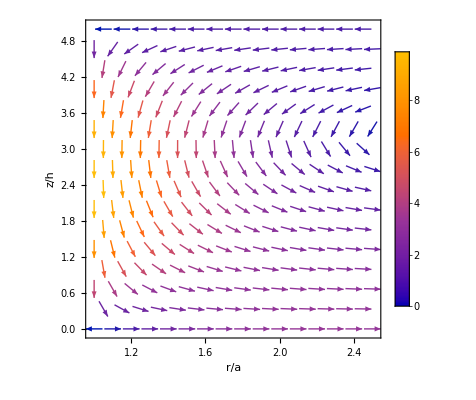

```mathematica
VectorPlot[Convert2d[r,0,z,1],{r,1,b},{z,0.0,5}, FrameLabel->{"r/a","z/h"},PlotLegends->Automatic]
```

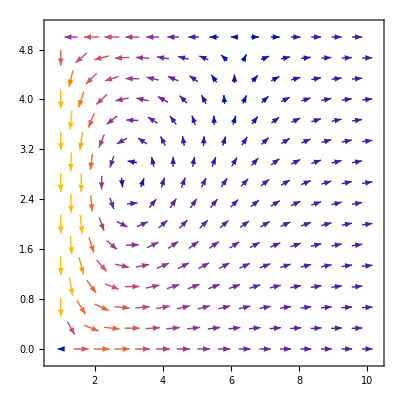

```mathematica
VectorPlot[{ur[r,z,0],uz[r,z,0]},{r,1,10},{z,0.0,5},VectorScaling->Automatic]
```

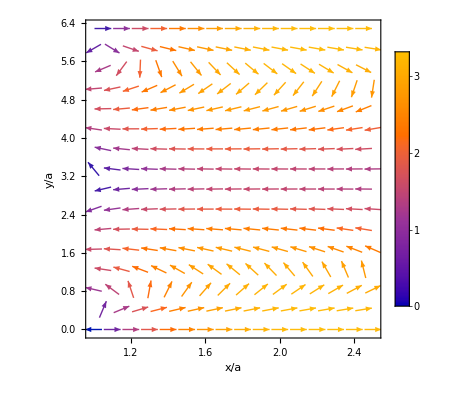

```mathematica
VectorPlot[Convert2dxy[r,θ,0,1],{r,1,b},{θ,0.0,2π}, FrameLabel->{"x/a","y/a"},PlotLegends->Automatic]
```

```mathematica
tfield=TransformedField["Cylindrical"->"Cartesian",{ur[r,θ,ζ],uθ[r,θ],uz[r,θ,ζ]}, {r,θ,ζ}->{x,y,z}];
```

```mathematica
VectorPlot3D[tfield,{x,-b,b*10},{y,-b,b},{z,0,1}]
```

-Graphics3D-

```mathematica
tp=TransformedField["Polar"->"Cartesian",{ur[r,θ,4],uθ[r,θ]}, {r,θ}->{x,y}];
```

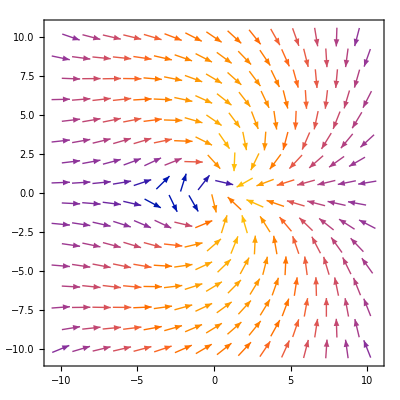

2.5

```mathematica
VectorPlot[tp, {x,-b,b}, {y,-b,b}]
```

```mathematica
Table[Convert2d[r,0,z,1],{r,1,4,0.1},{z,0,1.,0.1}]
```

{{{-9.62204×10^-19,0.},{-9.62204×10^-19,-1.34604},{-9.62204×10^-19,-2.68676},{-9.62204×10^-19,-4.01688},{-9.62204×10^-19,-5.33114},{-9.62204×10^-19,-6.62437},{-9.62204×10^-19,-7.89146},{-9.62204×10^-19,-9.1274},{-9.62204×10^-19,-10.3273},{-9.62204×10^-19,-11.4865},{-9.62204×10^-19,-12.6003}},{{1.24216,0.},{1.23981,-1.15455},{1.23277,-2.30454},{1.22108,-3.44543},{1.20476,-4.57273},{1.1839,-5.68198},{1.15857,-6.76881},{1.12887,-7.82893},{1.09492,-8.85814},{1.05686,-9.8524},{1.01482,-10.8078}},{{2.21579,0.},{2.21161,-0.990931},{2.1991,-1.97795},{2.1783,-2.95717},{2.14929,-3.92471},{2.11219,-4.87676},{2.06715,-5.80957},{2.01434,-6.71945},{1.95397,-7.60281},{1.88628,-8.45617},{1.81153,-9.27616}},{{2.97964,0.},{2.97404,-0.85039},{2.95726,-1.69742},{2.92938,-2.53776},{2.8905,-3.36808},{2.84078,-4.18511},{2.7804,-4.98562},{2.70962,-5.76645},{2.6287,-6.52453},{2.53797,-7.25686},{2.43779,-7.96055}},{{3.57705,0.},{3.57035,-0.729164},{3.55028,-1.45545},{3.51692,-2.17599},{3.4704,-2.88795},{3.41091,-3.58851},{3.33868,-4.2749},{3.25399,-4.94443},{3.15718,-5.59444},{3.04863,-6.22237},{2.92877,-6.82574}},{{4.04083,0.},{4.03329,-0.624251},{4.0107,-1.24604},{3.97315,-1.86291},{3.92078,-2.47243},{3.85382,-3.07219},{3.77251,-3.65982},{3.67718,-4.23302},{3.5682,-4.7895},{3.44602,-5.32709},{3.3111,-5.84365}},{{4.39632,0.},{4.38815,-0.533218},{4.36366,-1.06433},{4.32296,-1.59125},{4.2662,-2.11188},{4.19362,-2.62418},{4.10548,-3.12612},{4.00215,-3.61573},{3.88403,-4.09106},{3.75159,-4.55025},{3.60534,-4.99148}},{{4.66345,0.},{4.65481,-0.454069},{4.62894,-0.906346},{4.58594,-1.35505},{4.52596,-1.7984},{4.44926,-2.23465},{4.35614,-2.66209},{4.24696,-3.07902},{4.12215,-3.4838},{3.9822,-3.87482},{3.82768,-4.25056}},{{4.85809,0.},{4.84914,-0.385147},{4.82229,-0.768773},{4.77768,-1.14937},{4.71546,-1.52542},{4.63588,-1.89546},{4.53927,-2.25801},{4.42599,-2.61166},{4.29651,-2.955},{4.15132,-3.28667},{3.991,-3.60538}},{{4.99307,0.},{4.98391,-0.325065},{4.95644,-0.648847},{4.91078,-0.970068},{4.8471,-1.28746},{4.76567,-1.59977},{4.6668,-1.90577},{4.55088,-2.20425},{4.41836,-2.49403},{4.26978,-2.77396},{4.10572,-3.04295}},{{5.07884,0.},{5.06956,-0.272653},{5.04174,-0.544231},{4.99551,-0.81366},{4.93103,-1.07988},{4.84857,-1.34184},{4.74846,-1.5985},{4.63108,-1.84885},{4.4969,-2.0919},{4.34644,-2.3267},{4.18032,-2.55232}},{{5.12398,0.},{5.11466,-0.226918},{5.08673,-0.452941},{5.0403,-0.677176},{4.97557,-0.898739},{4.89277,-1.11675},{4.79224,-1.33036},{4.67438,-1.53872},{4.53965,-1.74101},{4.38858,-1.93642},{4.22177,-2.12419}},{{5.13561,0.},{5.12631,-0.18701},{5.09846,-0.373281},{5.05216,-0.55808},{4.9876,-0.740676},{4.90503,-0.920349},{4.80478,-1.09639},{4.68724,-1.2681},{4.55288,-1.43481},{4.40222,-1.59586},{4.23587,-1.75061}},{{5.11965,0.},{5.11043,-0.152197},{5.08281,-0.303794},{5.0369,-0.454192},{4.97288,-0.602797},{4.891,-0.749024},{4.79158,-0.892294},{4.67503,-1.03204},{4.54178,-1.16772},{4.39239,-1.29879},{4.22742,-1.42473}},{{5.08107,0.},{5.07197,-0.121852},{5.04471,-0.243222},{4.9994,-0.363633},{4.93621,-0.482608},{4.85539,-0.599679},{4.75727,-0.714384},{4.64223,-0.826269},{4.51073,-0.934893},{4.36328,-1.03983},{4.20046,-1.14066}},{{5.02403,0.},{5.01508,-0.0954259},{4.98829,-0.190475},{4.94374,-0.284773},{4.88163,-0.377946},{4.80219,-0.469628},{4.70573,-0.559457},{4.59264,-0.647078},{4.46337,-0.732145},{4.31842,-0.814322},{4.15837,-0.893286}},{{4.95204,0.},{4.94328,-0.0724457},{4.91703,-0.144605},{4.87339,-0.216195},{4.81254,-0.28693},{4.73472,-0.356534},{4.64023,-0.42473},{4.52944,-0.491251},{4.4028,-0.555832},{4.26081,-0.61822},{4.10402,-0.678168}},{{4.86808,0.},{4.85952,-0.0524969},{4.83388,-0.104787},{4.79126,-0.156663},{4.73183,-0.207921},{4.65582,-0.258358},{4.56353,-0.307776},{4.45532,-0.355979},{4.33163,-0.402777},{4.19294,-0.447985},{4.0398,-0.491426}},{{4.77466,0.},{4.76632,-0.0352171},{4.74135,-0.0702953},{4.69983,-0.105096},{4.64193,-0.139482},{4.56788,-0.173317},{4.47797,-0.206469},{4.37256,-0.238806},{4.25207,-0.2702},{4.11696,-0.300528},{3.96778,-0.329669}},{{4.6739,0.},{4.6658,-0.0202889},{4.64153,-0.0404978},{4.60117,-0.0605469},{4.5449,-0.080357},{4.47293,-0.0998499},{4.38555,-0.118949},{4.2831,-0.137578},{4.16599,-0.155665},{4.03467,-0.173137},{3.88968,-0.189926}},{{4.56762,0.},{4.55976,-0.00743324},{4.53621,-0.0148372},{4.49707,-0.0221825},{4.44249,-0.0294403},{4.37269,-0.0365819},{4.28793,-0.0435792},{4.18856,-0.0504044},{4.07497,-0.0570308},{3.9476,-0.063432},{3.80697,-0.069583}},{{4.45734,0.},{4.44973,0.00359556},{4.42693,0.00717692},{4.38904,0.01073},{4.33619,0.0142407},{4.26861,0.0176952},{4.18655,0.0210798},{4.09034,0.0243813},{3.98037,0.0275865},{3.85705,0.0306829},{3.72089,0.0336582}},{{4.34435,0.},{4.337,0.013014},{4.31496,0.0259766},{4.27833,0.0388367},{4.22726,0.0515436},{4.16193,0.064047},{4.08261,0.0762977},{3.98962,0.0882472},{3.88332,0.0998485},{3.76413,0.111056},{3.63251,0.121825}},{{4.22976,0.},{4.22266,0.0210132},{4.2014,0.0419435},{4.16604,0.0627083},{4.11674,0.0832256},{4.05369,0.103414},{3.97714,0.123195},{3.88739,0.14249},{3.78479,0.161222},{3.66975,0.179318},{3.54272,0.196706}},{{4.11449,0.},{4.10764,0.0277623},{4.08714,0.0554149},{4.05307,0.0828489},{4.00555,0.109956},{3.94478,0.136629},{3.87099,0.162763},{3.78448,0.188254},{3.68559,0.213003},{3.5747,0.236911},{3.45226,0.259884}},{{3.9993,0.},{3.99271,0.0334106},{3.97298,0.0666894},{3.94017,0.0997049},{3.89443,0.132327},{3.83592,0.164427},{3.76489,0.195878},{3.6816,0.226556},{3.5864,0.256339},{3.47965,0.285111},{3.36178,0.312758}},{{3.88486,0.},{3.87852,0.0380907},{3.85955,0.0760311},{3.828,0.113671},{3.78401,0.150863},{3.72775,0.18746},{3.65944,0.223316},{3.57935,0.258291},{3.4878,0.292247},{3.38515,0.32505},{3.2718,0.356569}},{{3.7717,0.},{3.76562,0.04192},{3.74738,0.0836745},{3.71708,0.125099},{3.67482,0.166029},{3.62077,0.206305},{3.55515,0.245766},{3.47822,0.284257},{3.39027,0.321627},{3.29165,0.357727},{3.18277,0.392415}},{{3.66027,0.},{3.65443,0.0450024},{3.63693,0.0898273},{3.60785,0.134298},{3.56729,0.178238},{3.51542,0.221475},{3.45244,0.263838},{3.3786,0.305159},{3.29419,0.345276},{3.19955,0.384031},{3.09504,0.42127}},{{3.55094,0.},{3.54534,0.0474305},{3.52856,0.0946737},{3.50067,0.141543},{3.46178,0.187854},{3.41204,0.233424},{3.35165,0.278073},{3.28084,0.321624},{3.1999,0.363905},{3.10915,0.404751},{3.00894,0.443999}},{{3.444,0.},{3.43864,0.049286},{3.42256,0.0983775},{3.39584,0.147081},{3.35857,0.195204},{3.31092,0.242556},{3.25305,0.288951},{3.18521,0.334206},{3.10766,0.378142},{3.0207,0.420585},{2.92468,0.461369}}}

```mathematica
Δt=0.1;
```

```mathematica
start = {0.1,0.1,5.0};
times = Table[Δt * i, {i,100}];
```

```mathematica
points=Map[Convert[start[[1]],start[[2]],start[[3]],#]&,times]
```

{{0.1 (0.00996671+0.995004 (-0.995004+16.5119 (-(2.89956 BesselK[0,a π])/BesselK[1,a π]^2+0.133031/(a BesselK[1,a π])))),0.1 (-0.0993347+1),-1.01106×10^-15 (0.289956/(a BesselK[1,a π])-(0.423452 1)/(a 1^2))},98,{1}}
 |  |  |  |

```mathematica
points=NestList[Convert[#[[1]],#[[2]],#[[3]],0.0001]&,start,100];
```

```mathematica
ListPointPlot3D[Re[points],PlotRange->All]
```

-Graphics3D-

```mathematica
ψ[x_,y_]:= y-y/(x^2+y^2)
```

```mathematica
u = D[ψ[x,y], y]
```

1+(2 y^2)/((x^2+y^2)^2)-1/(x^2+y^2)

```mathematica
v=-D[ψ[x,y], x]
```

-(2 x y)/((x^2+y^2)^2)

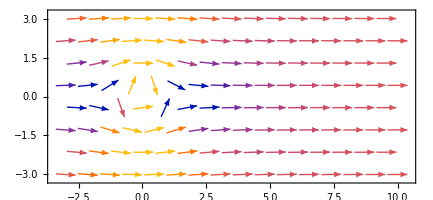

```mathematica
VectorPlot[{u,v}, {x,-3.0,10.0},{y,-3.0,3.0}, PlotLegends->Automatic,Axes->True,AspectRatio->True]
```

```mathematica
Clear[U]
```

```mathematica
ϕ[r_,θ_] := U(r+a^2/r)Cos[θ];
ϕr = D[ϕ[r,θ], r]
```

(1-1/r^2) U Cos[θ]

```mathematica
ϕθ = D[ϕ[r,θ], θ]
```

-((1/r+r) U Sin[θ])

```mathematica
With[{U=1},VectorPlot[{ϕr,ϕθ},{r,0.1,4}, {θ,0,π}]]
```

-Graphics-

```mathematica
ϕr*Sin[θ] + ϕθ Cos[θ]*1/r
```

10 (1-1/r^2) Cos[θ] Sin[θ]-(10 (1/r+r) Cos[θ] Sin[θ])/r

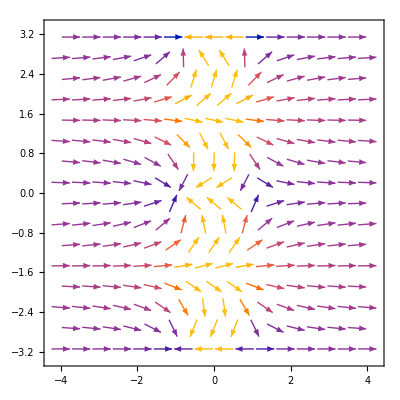

```mathematica
VectorPlot[{ϕr*Cos[θ] -ϕθ Sin[θ]*1/r,ϕr*Sin[θ] + ϕθ Cos[θ]*1/r},{r,-4,4}, {θ,-π,π}]
```

```mathematica
Clear[U,a]
```

```mathematica
Φ[x_,y_] := U x + U * a^2 x/(x^2+y^2)
```

```mathematica
Φx = D[Φ[x,y], x]
```

U-(2 a^2 U x^2)/((x^2+y^2)^2)+(a^2 U)/(x^2+y^2)

```mathematica
Φy = D[Φ[x,y], y]
```

-(2 a^2 U x y)/((x^2+y^2)^2)

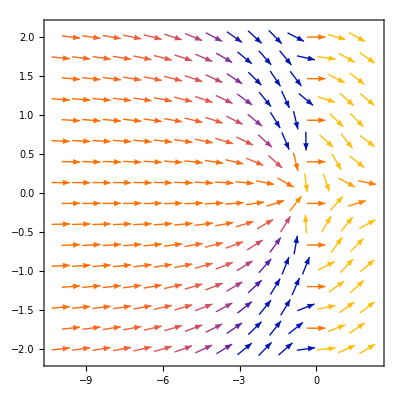

```mathematica
VectorPlot[{Φx ,Φy},{x,-10,2},{y,-2,2}]
```

```mathematica
∫Φxⅆy
```

U y-(a^2 U y)/(x^2+y^2)

```mathematica
u = ∂_y %
```

U+(2 a^2 U y^2)/((x^2+y^2)^2)-(a^2 U)/(x^2+y^2)

```mathematica
-∫Φyⅆx
```

-y/(x^2+y^2)

```mathematica
v = ∂_x %108
```

(2 a^2 U x y)/((x^2+y^2)^2)

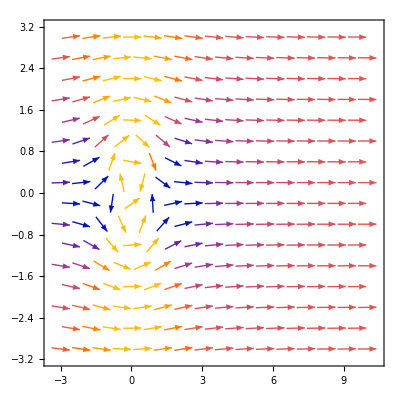

```mathematica
U=10;a=1;
VectorPlot[{u,-v}, {x,-3.0,10.0},{y,-3.0,3.0}]
```